```mathematica
{{m1= Import["C:\\GitHub\\metod_ustanovleniya\\m1.csv"];}, {m2= Import["C:\\GitHub\\metod_ustanovleniya\\m2.csv"];}}
```

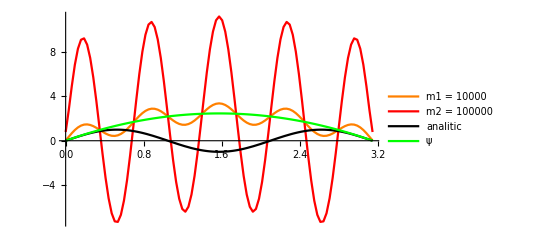

```mathematica
(*tau = 0.00000001
h = 100/π
m1 = 10000
m2 = 100000*)
Sol= DSolve[{u''[x] + 9 Sin[3 x]==0 && u[0]==0&&u[π]==0},u[x],x]; 
SolF = (u[x]/.{Sol1})[[1,1]];
ψ[x_] := x(π-x); ψplot = Plot[ψ[x],{x,0,π}, PlotStyle -> Green, PlotLegends-> {"ψ"}];
SolFPlot = Plot[Sol1F,{x,0,π}, PlotStyle -> Black,PlotLegends-> {"analitic"}];
plotm1 =ListLinePlot[m1, PlotStyle -> Orange,PlotLegends-> {"m1 = 10000"}];
plotm2 =ListLinePlot[m2, PlotStyle -> Red,PlotLegends-> {"m2 = 100000"}];
Show[plotm1, plotm2,SolFPlot, ψplot,PlotRange -> All]
```